```mathematica
im2real[x_]:={Re@x,Im@x};
real2im@{x_,y_}:=x+y*I;
```

```mathematica
(*f[x_] is the parametrization of the rectangle]*)
f[x_]=Piecewise[{{Sqrt[2]/2+(x-Sqrt[2]/2)*I,0<=x<=Sqrt[2]},{(3Sqrt[2]/2-x)+Sqrt[2]/2*I,Sqrt[2]<x<=2*Sqrt[2]},{-Sqrt[2]/2+(5Sqrt[2]/2-x)*I,2*Sqrt[2]<x<=3*Sqrt[2]},{x-7Sqrt[2]/2+(-Sqrt[2]/2)*I,3*Sqrt[2]<x<=4*Sqrt[2]}},Infinity];
points=Table[f@x,{x,0,4*Sqrt[2],0.01}];
```

```mathematica
Min@Table[Norm@x,{x,points}]
a0=First@MinimalBy[points,Norm]
```

0.707107

0.000252532-0.707107 ⅈ

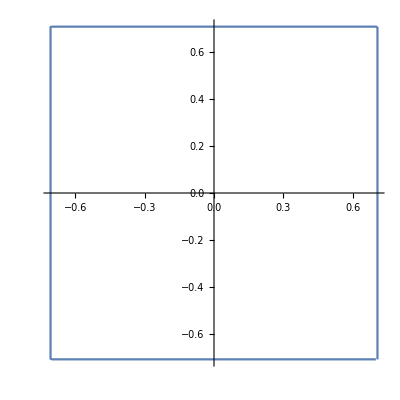

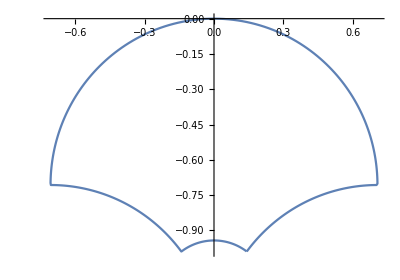

```mathematica
ListPlot[ReIm@points,AspectRatio->Automatic,Joined->True]
(*g[x_]=(x+Sqrt[2]/2)/(1+x Sqrt[2]/2);*)
g[x_]:=(x+a0)/(1+x*Conjugate[a0]);
points = g/@points;
ListPlot[ReIm@points,AspectRatio->Automatic,Joined->True]
```

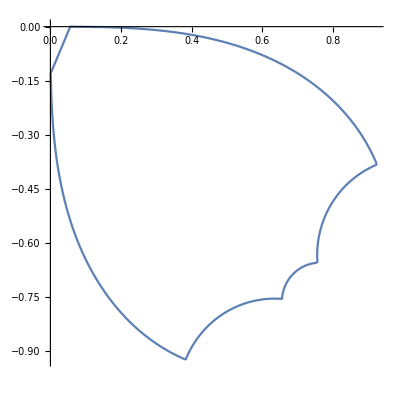

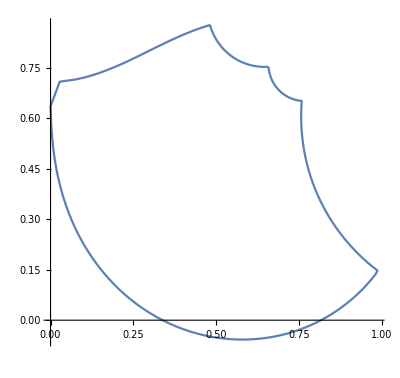

```mathematica
points = Sqrt/@points;
ListPlot[ReIm@points,AspectRatio->Automatic,Joined->True]
(*b0 = Sqrt[Sqrt[2]/2];*)
b0=g[0];
h[x_] := (x-b0)/(1-Conjugate[b0]*x);
points = h/@points;
(*points//.{x_List}:>x*)
points//.{x_List}:>x;
ListPlot[ReIm@points,AspectRatio->Automatic,Joined->True]
```

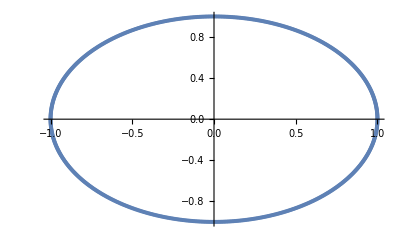

```mathematica
disk=Table[Cos[x/100]+I*Sin[x/100],{x,0,628}];
ListPlot[ReIm@disk]
```

```mathematica
points=Table[f@x,{x,0,4*Sqrt[2],0.01}];
i=0;
While[i<10,i++;
Print@Min@Table[Norm@x,{x,points}];
a0=First@MinimalBy[points,Norm];
g[x_]:=(x+a0)/(1+x*Conjugate[a0]);
points=g/@points;
"S";
points=points/(a0/Norm@a0);
"Spin";
points=Sqrt/@points;
points=points*(a0/Norm@a0);
b0=g[0];
h[x_] := (x-b0)/(1-Conjugate[b0]*x);
points=h/@points;
ListPlot[{Labeled[ReIm@points,"points"],Labeled[ReIm@disk,"disk"]},AspectRatio->Automatic,Joined->True]
]
```

0.707107

0.596671

0.683384

0.722713

0.722968

0.647616

0.760684

0.731914

0.800965

0.787461

```mathematica
points=Table[f@x,{x,0,4*Sqrt[2],0.01}];
```

0.707107

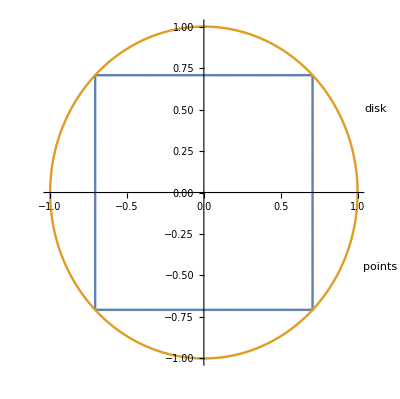

0.596671

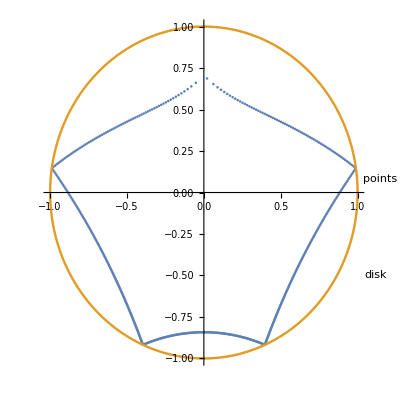

```mathematica
Print@Min@Table[Norm@x,{x,points}];
ListPlot[{Labeled[ReIm@points,"points"],Labeled[ReIm@disk,"disk"]},AspectRatio->Automatic]
a0=First@MinimalBy[points,Norm];
g[x_]:=(x+a0)/(1+x*Conjugate[a0]);
points=g/@points;
points=points/(a0/Norm@a0);
points=Sqrt/@points;
points=points*(a0/Norm@a0);
b0=g[0];
h[x_] := (x-b0)/(1-Conjugate[b0]*x);
points=h/@points;
Print@Min@Table[Norm@x,{x,points}];
ListPlot[{Labeled[ReIm@points,"points"],Labeled[ReIm@disk,"disk"]},AspectRatio->Automatic]
```